```mathematica
(*
1) Выполнить обучающую модель,используя команду Manipulate,по теме
«Построение графика квадратичной функции f(x) = a*x + b*x + c ».Показать
график в зависимости от параметров a,b,c.Использовать разные элементы
управления.Оформить в удобном для пользователя виде.
*)

Manipulate[Plot[a*x^2+b*x+c,{x,-20,20},PlotRange->{-20,20}],{a,0,5},{b,0,5},{c,0,5}]
```

```mathematica
Manipulate[Plot[a*x^2+b*x+c,{x,-20,20},PlotRange->{-20,20}],{a,{0,1,2,3,4,5,6,7,8,9,10}},{b,{0,1,2,3,4,5,6,7,8,9,10}},{c,{0,1,2,3,4,5,6,7,8,9,10}}]
```

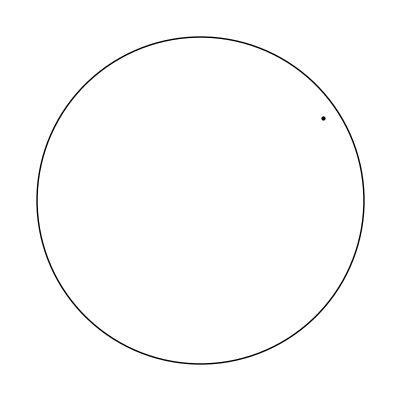

```mathematica
(*
2) Пользователь вводит координаты точки на плоскости.Программа
должна определить,принадлежит ли точка заданной области координатной
плоскости.Продемонстрировать с помощью чертежа.Объяснить работу.Области принадлежат точки,лежащие во второй координатной четверти и
x 2  y 2  16 внутри окружности.
*)

Show[{Graphics[Circle[{0,0},4]],Graphics[Point[{3,2}]]}]
```



```mathematica
Graphics[Circle[{0,0},4]]
```